```mathematica
r=3.3;
```

```mathematica
f[x_]:=r*x*(1-x);
```

```mathematica
G=f[f[x]];
```

```mathematica
Solve[G==x]
```

{{x→0.},{x→0.479427},{x→0.69697},{x→0.823603}}

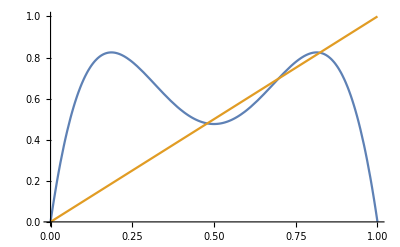

```mathematica
Plot[{G,x},{x,0,1}]
```

```mathematica
Abs[f'[0.479427]*f'[0.823603]]
```

0.29

```mathematica
r=3.54409;
```

```mathematica
H=f[f[f[f[x]]]];
```

```mathematica
roots=FindInstance[H==x,x,Reals,10]//N
```

{{x→0.},{x→0.36329},{x→0.419248},{x→0.523595},{x→0.71784},{x→0.819785},{x→0.862911},{x→0.88405}}

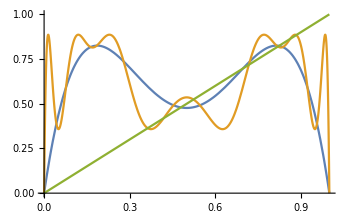

```mathematica
Plot[{G,H,x},{x,0,1}]
```

```mathematica
Abs[f'[0.36329047193813774]*f'[0.5235946278390694]*f'[0.8197854155285317]*f'[0.8840498586324046]]
```

0.999993

```mathematica
r=3.544091;
```

```mathematica
Abs[f'[0.3632900979203472]*f'[0.5235950731877871]*f'[0.8197853549757883]*f'[0.884050197407276]]
```

1.00002